```mathematica
(* LOAD VARIABLES ----------------------
loads all functions and data (made in this file and evaluated previously) into memory so you don't have to run them again *)
Get[StringReplace[NotebookFileName[],".nb"->", variables.mx"]];
```

Get::noopen: Cannot open TraditionalForm`"C:\\Users\\Omar\\Dropbox\\Academic\\Projects\\7.Two Qubit Bloch Space\\Code\\10.Basic Entangler SV Plots, variables.mx".

```mathematica
(* SAVE VARIABLES ----------------
Save the variables after evaluating them initially so you don't have to re-evaluate them every time *)
DumpSave[StringReplace[NotebookFileName[],".nb"->", variables.mx"],"Global`"];
```

```mathematica
(* LOAD BLOCH SVD FUNCTIONS ---------------- *)
(* Get[NotebookDirectory[]<> "BlochSVD.m"]; *)
<<BlochSVD`
```

```mathematica
(* takes an svd, return a vector of 4 entries, first 3 are the singular value, last is 0 or .1 flag for separable/entangled *)
ReturnSVFlag[svd_]:=Module[{svdPH,svs,flag,g,M,Σ,N,h},
{{g},M,Σ,N,{h}}=svd;
svs=Diagonal[Σ];
svdPH={{g},-M,Σ,N,{h}}; (* PH criterion *)
(*flag=If[MemberQ[Sign[ineqLHS[svdPH]],-1],.1,0];*) 
(*Join[svs,{flag}]*)
Join[svs,ineqLHS[svdPH][[2;;3]]]
]
```

```mathematica
ReturnSVMod[svd_]:=Module[{svdPH,svs,flag,g,M,Σ,N,h},
{{g},M,Σ,N,{h}}=svd;
svs=Diagonal[Σ];
svdPH={{g},-M,Σ,N,{h}}; (* PH criterion *)
(*flag=If[MemberQ[Sign[ineqLHS[svdPH]],-1],.1,0];*) 
(*Join[svs,{flag}]*)
Join[svs,g,h]
]
```

```mathematica
PH[svd_]:=Module[{svdPH,g,M,Σ,N,h},
{{g},M,Σ,N,{h}}=svd;
svdPH={{g},-M,Σ,N,{h}}; (* PH criterion *)
ineqLHS[svdPH][[2;;3]]
]
```

```mathematica
ReturnSV[svd_]:=Diagonal[svd[[3]]];
```

```mathematica
ReturnSVQuantities[svd_]:={Norm[Diagonal[svd[[3]]]],Det[svd[[2]].svd[[3]].svd[[4]]],Tr[({{1, 0, 0}, {0, 1, 0}, {0, 0, Det[svd[[2]].svd[[4]]]}}).svd[[3]]]};
```

```mathematica
(* baseθvec is the one multplied by coefficient plotted on the horizontal axis of the graph *)
PlotSValues[rhoInit_,baseθvec_]:= Plot[{ReturnSV[#]}&[ApplyBasicEntangleU[c baseθvec,rho2svd[rhoInit]]],{c,-Pi,Pi},ImageSize->800,PlotStyle->Thickness[.003]];
```

```mathematica
(* each row of baseθmatrix is baseθvec for an entry in the graphics row *)
GraphicsRowSValues[rhoInit_,baseθmatrix_]:=GraphicsRow[Table[PlotSValues[rhoInit,vec],{vec,baseθmatrix}],ImageSize->Full];
```

```mathematica
FlexPlotSValues[rhoInit_]:=Manipulate[PlotSValues[rhoInit,{baseθvec1,baseθvec2,baseθvec3}],{baseθvec1,-1,1},{baseθvec2,-1,1},{baseθvec3,-1,1}];
```

```mathematica
(* meant to plot quantities derived from the singular values, no the singular values themselves *)
FlexPlotSValuesss[mat_]:=Manipulate[With[{n=5},Plot[Evaluate[Hold[ReturnSVFlag[ApplyBasicEntangleU[c {vec1,vec2,vec3},rho2svd[mat]]][[#]]]&/@Range[5]],{c,-Pi,Pi},ImageSize->800]],{vec1,-1,1},{vec2,-1,1},{vec3,-1,1}];
```

```mathematica
(* plot how singular values change with the entangling parameters *)
```

```mathematica
(* GRAPHICS ROW - for some standard combinations *)
```

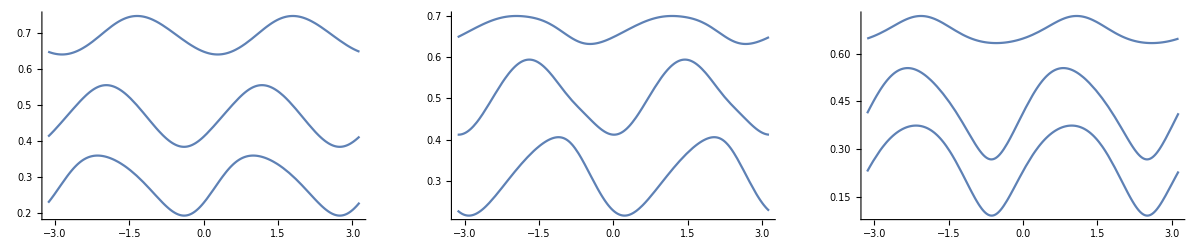

```mathematica
GraphicsRowSValues[rho0,IdentityMatrix[3]]
```

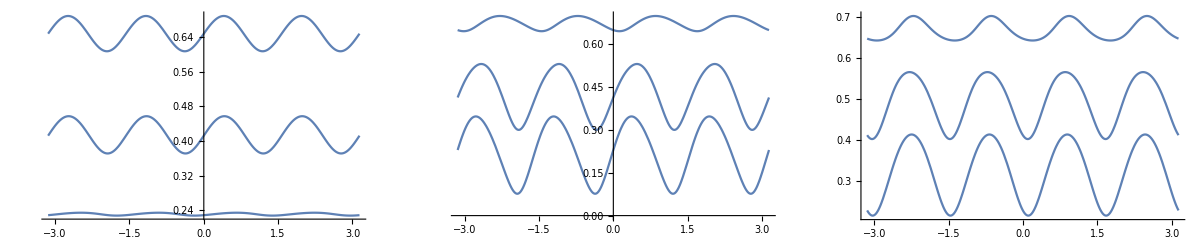

```mathematica
(* this one is very interestingly periodic for all, with period Pi/2 --- could this one be the key to a simple representation of the effect of this operation on the SVD ? *)
GraphicsRowSValues[rho0,1-2IdentityMatrix[3]]
```

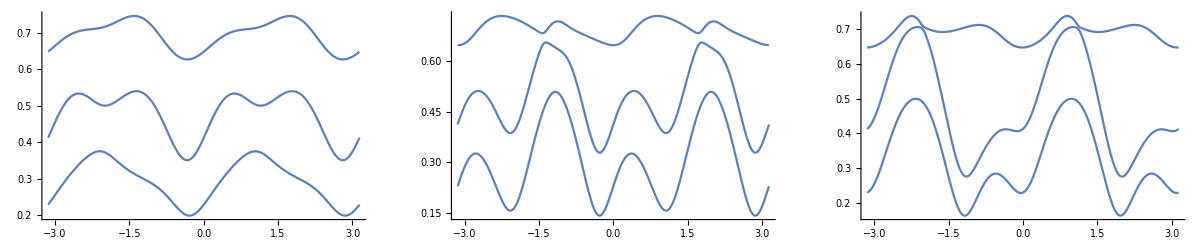

```mathematica
(* varying the c-parameterization in right combinations is same as varying d-parameterization *)
GraphicsRowSValues[rho0,1-IdentityMatrix[3]]
```

```mathematica
(* WITH RANDOM ORTHOGONAL ... to create avoided crossings *)
```

```mathematica
(* they look like avoided crossings, bu why? there can be degeneracy in singular values ... sometimes avoided, sometimes  they cross, when does each happen? related to entanglement? *)
```

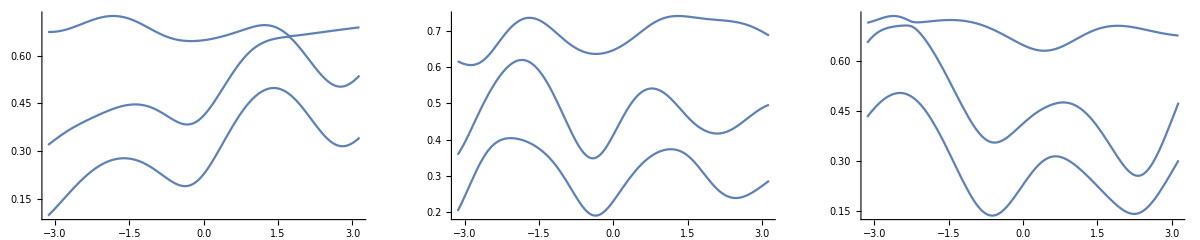

```mathematica
GraphicsRowSValues[rho0,RO[3]]
```

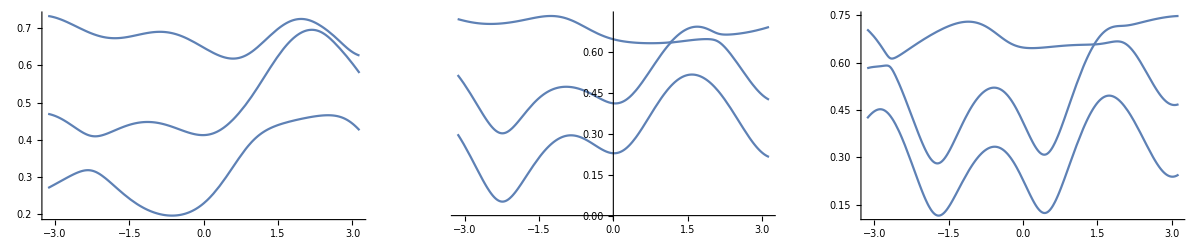

```mathematica
GraphicsRowSValues[rho0,RO[3]]
```

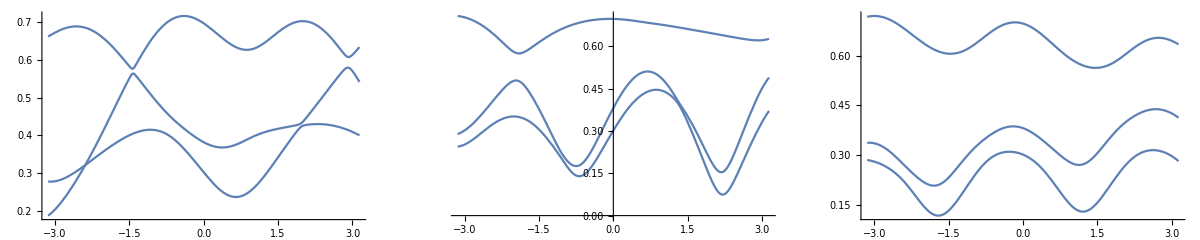

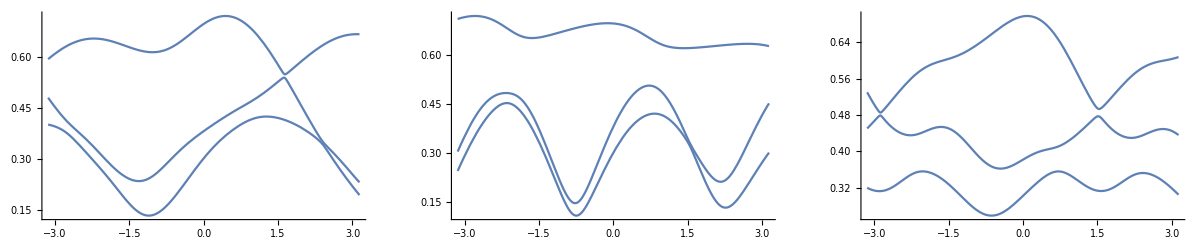

```mathematica
(* an avoided crossing if there ever was one! *)
```

```mathematica
(* FLEXPLOTSVALUES *)
```

```mathematica
FlexPlotSValues[rho0]
```

Part::partw: Part TraditionalForm`3 of TraditionalForm` does not exist.

Diagonal::list: List expected at position TraditionalForm`1 in TraditionalForm`.

Part::partw: Part TraditionalForm`3 of TraditionalForm` does not exist.

Diagonal::list: List expected at position TraditionalForm`1 in TraditionalForm`.

Part::partw: Part TraditionalForm`3 of TraditionalForm` does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Diagonal::list: List expected at position TraditionalForm`1 in TraditionalForm`.

General::stop: Further output of Diagonal :: list will be suppressed during this calculation.

```mathematica
(* So the "avoided crossings" can be converted to actual crossings and vice versa by changing the parameters a little .... 
when avoided crossings happen, we already showed two of M and N axes rotated Pi/2 to "switch" the axes of the singular values... 
when the actual crossing the Pi/2 rotation takes place instantly ... because at the degenerate crossing point, any rotation works *)
```

```mathematica
(* is there any interesting physical effect at these avoided/realized crossings, or is this just a mathematical curiosity 
If there is any physical meaning, it is unrelated to entanglement ... which pops up in places with or without crossings 
Entangled regions seem centred on regions with local maxima of the highest singular value (but not all such regions)
*)
(* even when periodic they are not sine waves... but the peaks are wider than the troughs ...
```

```mathematica
(* EXPLORE THIS COEFFICIENT MATRIX *)
```

```mathematica
(* I thought it gives nicee results, but it gives strange results, lots of avoided crossings. Only saving grace its more periodic, but that doesn't matter much ..*)
```

```mathematica
coeff=1-2IdentityMatrix[3]
```

(-1 | 1 | 1
1 | -1 | 1
1 | 1 | -1)

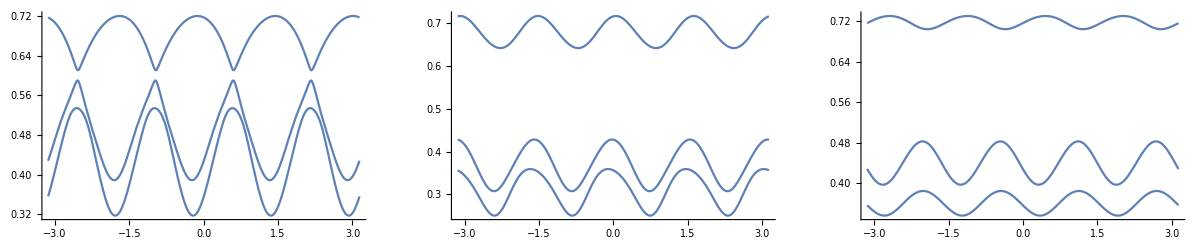

```mathematica
GraphicsRowSValues[RDM[4],coeff]
```

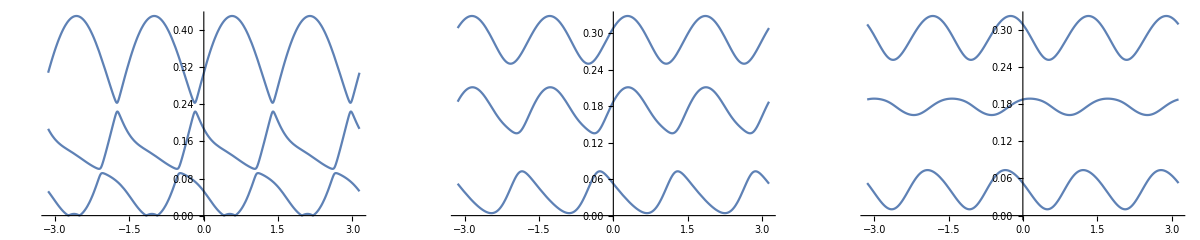

```mathematica
GraphicsRowSValues[RDM[4],coeff]
```

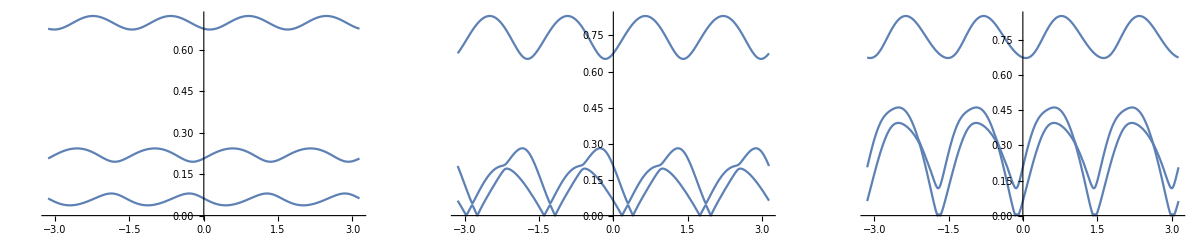

```mathematica
GraphicsRowSValues[RDM[4],coeff]
```

```mathematica
(* I am now convinced that if a "simple basis" of θvec exists, with a simple effect on the SVs, then it is one that will depend on the state rho, will not be generically the same for all rho ... what could it be then? imagine it as a unit vector n dotted with (Subscript[σ, 1]⊗Subscript[σ, 1],Subscript[σ, 2]⊗Subscript[σ, 2],Subscript[σ, 3]⊗Subscript[σ, 3]) followed by a matrix exponential ... *)
```

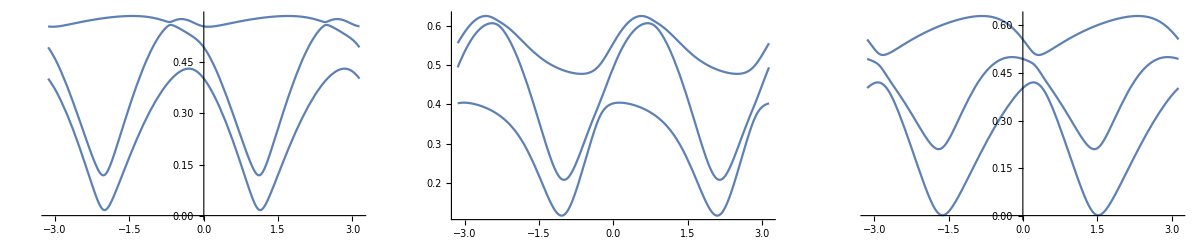

```mathematica
ρrandom=RDM[4];
GraphicsRowSValues[ρrandom,IdentityMatrix[3]]
```

```mathematica
(* try a diagonal R *)
```

```mathematica
ineqLHS[r2svd[rdiag]]
```

```mathematica
rdiag=({{1, -.2, -.3, 0}, {-.1, .25, 0, 0}, {.2, 0, -.4, 0}, {.1, 0, 0, .2}});
```

```mathematica
ineqLHS[r2svd[rdiag]]
```

{2.5475,0.6455,0.450856}

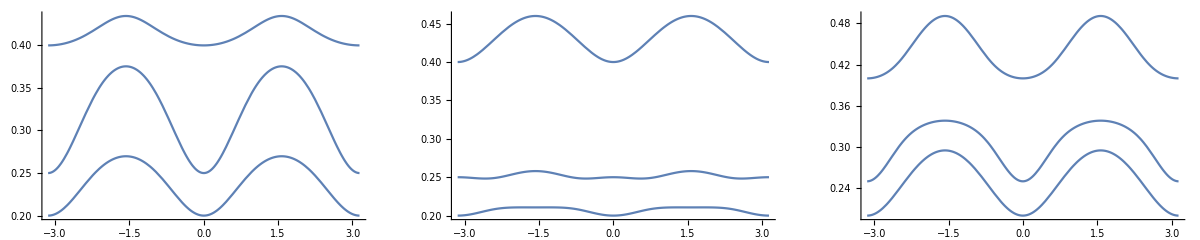

```mathematica
GraphicsRowSValues[r2rho[rdiag],IdentityMatrix[3]]
```

```mathematica
ralmostdiag=({{1, -.2, -.3, 0}, {-.1, .25, 0, 0}, {.2, 0, -.4, .1}, {.1, 0, -.15, .2}});
```

```mathematica
ineqLHS[r2svd[ralmostdiag]]
```

{2.515,0.6145,0.4079}

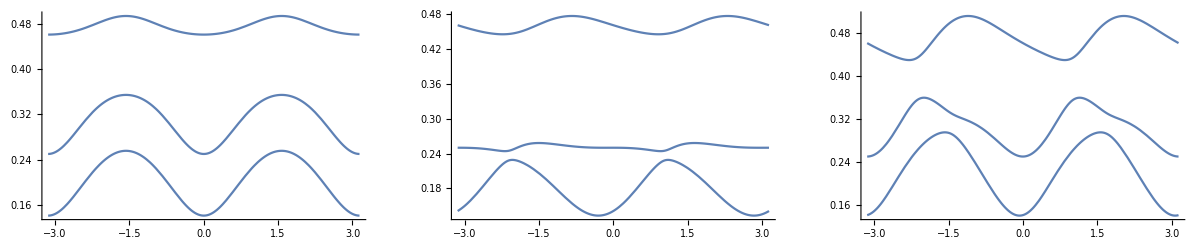

```mathematica
GraphicsRowSValues[r2rho[ralmostdiag],IdentityMatrix[3]]
```

```mathematica
ralmostdiag2=({{1, -.2, -.3, 0}, {-.1, .25, 0, -.1}, {.2, 0, -.4, .1}, {.1, -.1, .1, .2}});
```

```mathematica
ineqLHS[r2svd[ralmostdiag2]]
```

{2.5075,0.6005,0.378056}

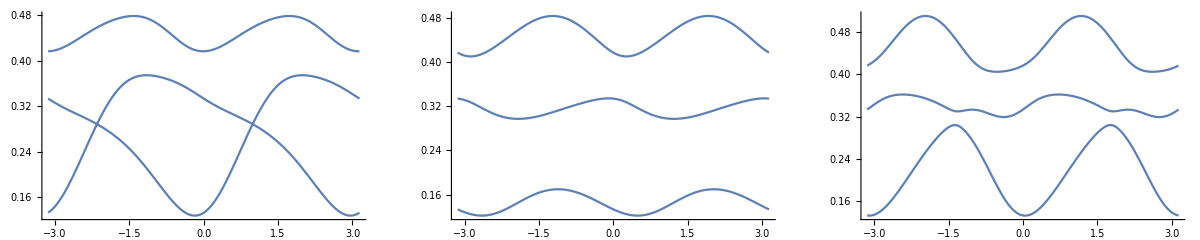

```mathematica
GraphicsRowSValues[r2rho[ralmostdiag2],IdentityMatrix[3]]
```

```mathematica
(* interesting, in basis where R is diagonal ... it is periodic with aligned peaks and troughs ... it is nice and periodic whenever 4 offdiagonal entries in the ith rho and ith column are zero.
Even then then the only real advantage you get from diagonal or almost diagonal is that the peak becomes symmetric, though no simple geometric picture emerges
but problem is rho is not generally diagonal or "almost diagonal".. the correct strategy would be to customize not rho, but the basis in span(Subscript[σ, 1]⊗Subscript[σ, 1],Subscript[σ, 2]⊗Subscript[σ, 2],Subscript[σ, 3]⊗Subscript[σ, 3]) ... note that a local operation on rho cannot be reduced to changing the linear combinaiton of (Subscript[σ, 1]⊗Subscript[σ, 1],Subscript[σ, 2]⊗Subscript[σ, 2],Subscript[σ, 3]⊗Subscript[σ, 3]) *)
```

```mathematica
(* let us try to find this for some rho *)
```

```mathematica
rho0
```

(0.311401 | -0.0463452-0.0655502 ⅈ | -0.0801704-0.0276297 ⅈ | 0.00694287-0.0612873 ⅈ
-0.0463452+0.0655502 ⅈ | 0.230523 | -0.0103691-0.115779 ⅈ | 0.0203704+0.0643149 ⅈ
-0.0801704+0.0276297 ⅈ | -0.0103691+0.115779 ⅈ | 0.26885 | 0.0798066-0.0990544 ⅈ
0.00694287+0.0612873 ⅈ | 0.0203704-0.0643149 ⅈ | 0.0798066+0.0990544 ⅈ | 0.189227)

```mathematica
rho2r[rho0]
```

(1. | 0.0669227 | 0.329209 | 0.160501
-0.1196 | -0.00685252 | -0.108984 | -0.201082
-0.0733704 | 0.354133 | -0.034624 | 0.183889
0.0838473 | -0.252304 | -0.0670083 | 0.00125533)

```mathematica
rho2svd[rho0]
```

{(0.0788653 | -0.142835 | -0.00980931),(0.205444 | 0.929791 | 0.30542
-0.844417 | 0.0106518 | 0.53558
0.494724 | -0.367934 | 0.78732),(0.468983 | 0 | 0
0 | 0.220172 | 0
0 | 0 | 0.111846),(-0.906779 | 0.409824 | -0.0989782
-0.0560863 | -0.349935 | -0.935093
-0.41786 | -0.842372 | 0.340299),(-0.146215 | -0.222977 | -0.259847)}

```mathematica
FlexPlotSValues[rho0]
```

```mathematica
FlexPlotSValues[rhoBell]
```

```mathematica
FlexPlotSValues[rhopure]
```

```mathematica
(* for both Bell and pure state you get only two inque singula values, consequence of purity .. 
for Bell you have what looks like a sin wave, not so for pure since valleys are narrow *)
```

```mathematica
FlexPlotSValues[rhoProduct]
```

```mathematica
(* GRAPH FOR EXPORT *)
```

```mathematica
ρrandom=RDM[4];
```

```mathematica
ρrandom
```

(0.391197 | 0.022472+0.0448939 ⅈ | -0.13709+0.0168835 ⅈ | -0.0662421-0.00441702 ⅈ
0.022472-0.0448939 ⅈ | 0.212445 | 0.0659379+0.0249117 ⅈ | -0.00601184-0.0406478 ⅈ
-0.13709-0.0168835 ⅈ | 0.0659379-0.0249117 ⅈ | 0.310221 | 0.00116247+0.0316406 ⅈ
-0.0662421+0.00441702 ⅈ | -0.00601184+0.0406478 ⅈ | 0.00116247-0.0316406 ⅈ | 0.0861376)

```mathematica
svaluesPlotgeneric=PlotSValues[ρrandom,{1,0,0}];
```

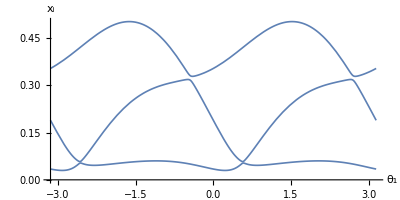

```mathematica
SValuesFigureXportgeneric=Show[svaluesPlotgeneric,{AxesOrigin->{-Pi,0},AxesLabel-> {Subscript[θ, 1],Subscript[x, i]},BaseStyle-> {FontSize->14}},ImageSize-> 400, AspectRatio->1/2]
```

```mathematica
Export[ParentDirectory[NotebookDirectory[]]<>  "\Lyx - Paper - v3\svalueU1generic.pdf",SValuesFigureXportgeneric]
```

C:\Users\Omar\Dropbox\Academic\Projects\7.Two Qubit Bloch Space\Lyx - Paper - v3\svalueU1generic.pdf

```mathematica
svaluesPlotpure=PlotSValues[rhopure,{1,0,0}];
```

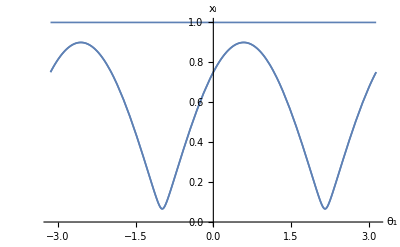

```mathematica
SValuesFigureXportpure=Show[svaluesPlotpure,{AxesLabel-> {Subscript[θ, 1],Subscript[x, i]}},ImageSize-> 400]
```

```mathematica
Export[ParentDirectory[NotebookDirectory[]]<>  "\Lyx - Paper - v1\svalueU1pure.pdf",SValuesFigureXportpure]
```

C:\Users\Omar\Dropbox\Academic\Projects\7.Two Qubit Bloch Space\Lyx - Paper - v1\svalueU1pure.pdf

```mathematica
svaluesPlotBell=PlotSValues[rhoBell,{1,0,0}];
```

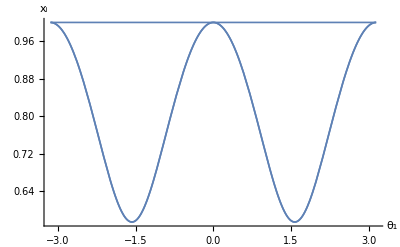

```mathematica
SValuesFigureXportBell=Show[svaluesPlotBell,{AxesLabel-> {Subscript[θ, 1],Subscript[x, i]}},ImageSize-> 400]
```

```mathematica
Export[ParentDirectory[NotebookDirectory[]]<>  "\Lyx - Paper - v1\svalueU1Bell.pdf",SValuesFigureXportBell]
```

C:\Users\Omar\Dropbox\Academic\Projects\7.Two Qubit Bloch Space\Lyx - Paper - v1\svalueU1Bell.pdf

```mathematica
rhoBell
```